# Mathematica

## May 2: Introduction to various functions

Plus and Times function: Even little children know what it does
Subtract function:

```mathematica
Subtract[a,b]
```

a-b

Lists:

```mathematica
list={1,2,3,4,5};
list = List[1,2,3,4,5]
```

{1,2,3,4,5}

Range Function-> Range[Start, Stop, Step] (Stop is EXCLUSIVE)
Also, Range[Something] = {1, 2, 3... Something]

```mathematica
Range[5]
Range[1,2,0.1]
```

{1,2,3,4,5}

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

List of ones or List of zeroes hacks:

```mathematica
Range[1,10]^0
Range[1,10]*0
```

{1,1,1,1,1,1,1,1,1,1}

{0,0,0,0,0,0,0,0,0,0}

But proper legal way:

```mathematica
Table[1,10]
```

{1,1,1,1,1,1,1,1,1,1}

Accessing particular element of list: Array [[]] (double square bracket)

```mathematica
list=  Range[10];
list[[5]]
```

5

## May 5: Function definitions, Mapping functions

Hold function-> doesn’t evaluate function

```mathematica
Hold[Plus[1, 1]]
```

Hold[1+1]

FullForm -> Prints the entire expression in full form. We need to use FullForm[Hold[Something]] to prevent mathematica from evaluate the damn thing.

```mathematica
FullForm[Hold[1 + 1 / 2 * 15 ^2]]
```

Hold[Plus[1,Times[Times[1,Power[2,-1]],Power[15,2]]]]

Postfix ->”//” -> applies function
Prefix -> “@ ()” -> applies function

```mathematica
1 + 2 // Hold // FullForm
FullForm@(Hold@(1 + 2))
```

Hold[Plus[1,2]]

Hold[Plus[1,2]]

Applying function to each element of array:
function / @ array

```mathematica
f /@({1,2,3})
```

{f[1],f[2],f[3]}

Defining our own function

```mathematica
f[x_, y_] = x * y (*Evaluates the function itself, which is why we see output of function itself*)
f[x_, y_] := x * y (* Doesn't evaluate the function right now, we don't see output of function itself*)
f[1,2]
```

x y

2

% -> apply something to output of previous input
%% -> two steps previous, etc.
Personally, NEVER USE THIS.

```mathematica
list = {1,2,3}
```

{1,2,3}

```mathematica
Reverse[%]
```

{4,3,2,1}

## May 5: Strings and Arrays

Dropping first n elements

```mathematica
StringDrop["string", 3]
```

ing

```mathematica
StringReplace["string", "t" -> "F"]
```

sFring

Import Text

```mathematica
(*Import["path"]
Export["path", data]*)
```

List -> Vector
Array -> Matrix -> just a nested list
Display using //MatrixForm
Visualizing lists: ListPlot function

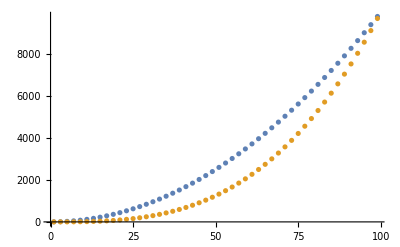

```mathematica
table1 = Table[{i, i^2}, {i, 1, 100, 2}];
table2  =  Table[{i, (i^3)/100}, {i, 1, 100, 2}];
ListPlot[{table1, table2}]
```

Things to do while plotting stuff:
- AxesLabel
- PlotLabel
- PlotLegends
- FrameLable
- Frame

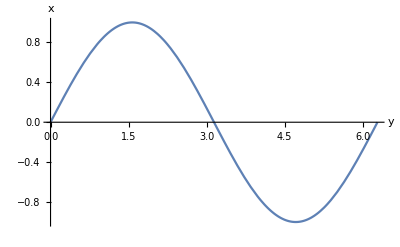

```mathematica
Plot[Sin[x], {x, 0, 2 * Pi}, AxesLabel-> {"y","x"}]
```

Log plots are nice!

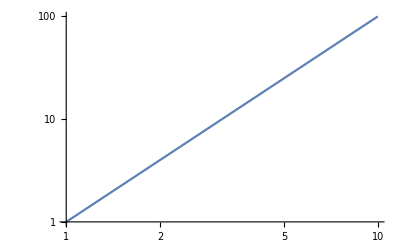

```mathematica
LogLogPlot[i^2,{i, 1, 10}]
```

Bottom line is, there are parametric plots, etc., many different kinds of plots
VectorPlot:

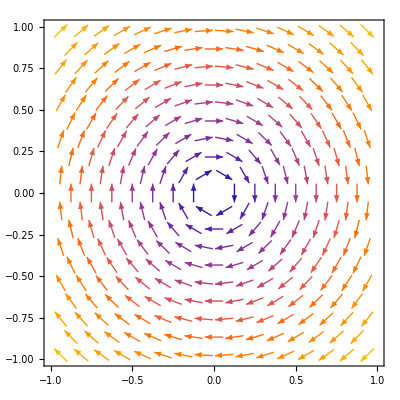

```mathematica
VectorPlot[{y, -x}, {x, -1, 1}, {y, -1, 1}]
```